Read data

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop-Debug"}]]
```

/home/v.korchagova/Документы/BMSTU/build-RKDG2D-Desktop-Debug

```mathematica
coeffs =Import["alphaCoeffs/0.002500","Table"];
mesh=Import["mesh2D","Table"];
```

```mathematica
hx=mesh[[1,3]]
hy=mesh[[2,3]]
MeshCellArea=hx*hy;
MeshCellRcm=mesh[[4;;]];
nCells=Length@MeshCellRcm;
alpha=Table[Partition[coeffs[[i]],3],{i,1,nCells}];
```

0.01

0.1

#### Construct form functions

```mathematica
Phi0[n_,r_]:=1./(√MeshCellArea)
Phi1[n_,r_List]:=√(12./(hy hx^3))(r[[1]]-MeshCellRcm[[n,1]])
Phi2[n_,r_List]:=√(12./(hy^3 hx))(r[[2]]-MeshCellRcm[[n,2]])
Phi[n_,r_List]:={Phi0[n,r],Phi1[n,r],Phi2[n,r]}
```

#### Reconstruct solution

```mathematica
GetSol[alpha_,n_,numSol_,r_List]:=Sum[Phi[n,r][[i]]alpha[[n,numSol,i]],{i,3}];
```

```mathematica
GetSolDensity[alpha_,n_,numSol_]:=Module[{pts,anSol},(
pts={{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]+hy/2.0},
{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]+hy/2.0}};
anSol=Table[GetSol[alpha,n,numSol,pts[[i]]],{i,1,4}];
Return[Table[{pts[[i,1]],pts[[i,2]],anSol[[i]]},{i,1,4}]]
)];
GetSolGraphics[alpha_,n_,numSol_]:=Module[{pts,anSol},(
pts={{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]+hy/2.0},
{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]+hy/2.0}};
anSol=Table[GetSol[alpha,n,numSol,pts[[i]]],{i,1,4}];
Return[Polygon@Table[{pts[[i,1]],pts[[i,2]],anSol[[i]]},{i,1,4}]]
)];
```

#### Draw solution

```mathematica
Graphics3D@Table[GetSolGraphics[alpha,i,1],{i,1,nCells}]
```

-Graphics3D-

```mathematica
bou=MeshCellRcm[[All,1]]-hx/2
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99}

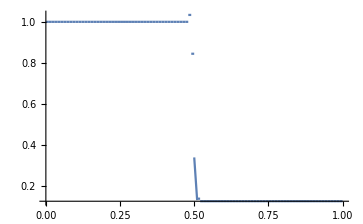

```mathematica
funVis1D[y_]:=Piecewise[Table[{GetSol[alpha,i,1,{0,y}],MeshCellRcm[[i,2]]-hy/2.0 < y <MeshCellRcm[[i,2]]+hy/2.0},{i,1,nCells}]];
funVis1D[x_]:=Piecewise[Table[{GetSol[alpha,i,1,{x,0}],MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,1,nCells}]];
fig=Plot[funVis1D[x],{x,0,1},Exclusions->bou,PlotPoints->200,PlotRange->All]
```

```mathematica
troubledCells={47,49,50,51}+1
funVis1DLim[x_]:=Piecewise[Table[{GetSol[alpha,i,1,{x,0}],MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,troubledCells}]];
```

{48,50,51,52}

```mathematica
trb=Plot[funVis1DLim[x],{x,0,1},PlotStyle->Red,Exclusions->bou,PlotPoints->200];
```

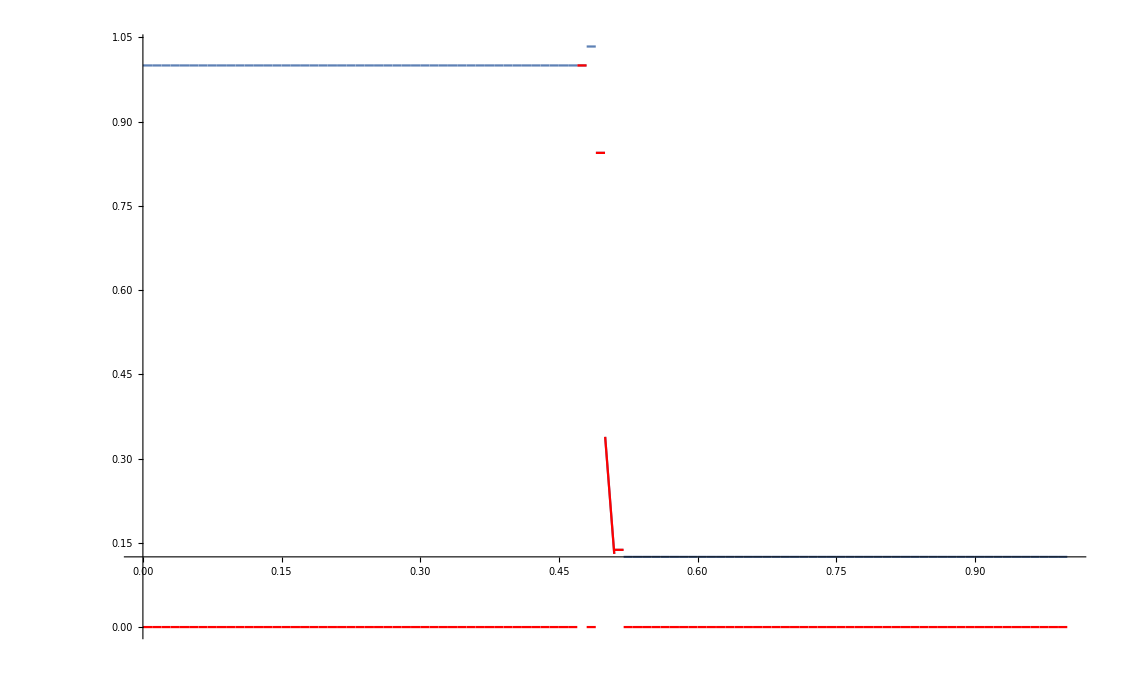

```mathematica
Show[fig,trb]
```

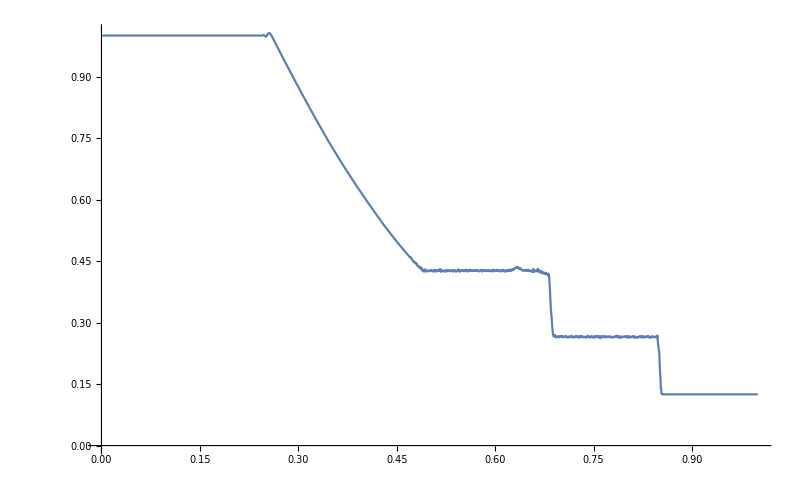
```mathematica
(*MUSCL, 1000 cells*)
-Graphics-
```

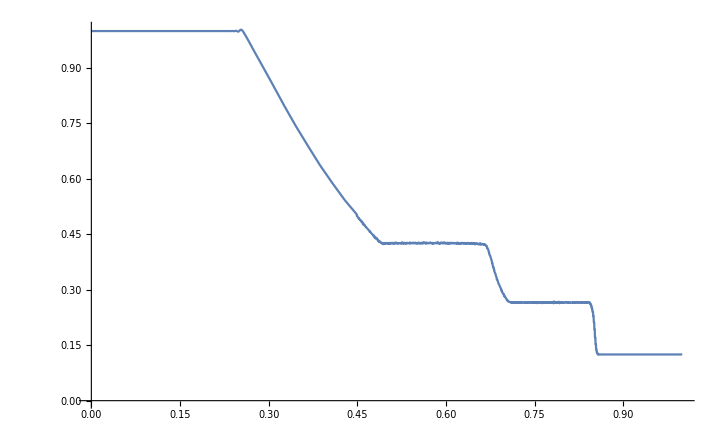
```mathematica
(*FinDiff, 1000 cells*)
-Graphics-
```

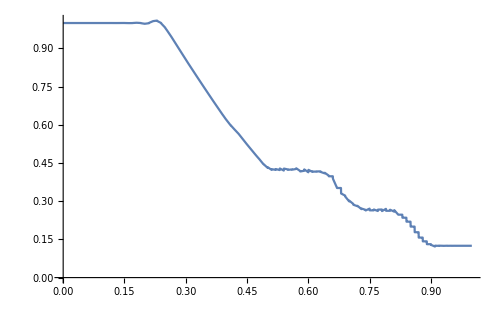
```mathematica
(*FinDiff, 100 cells*)
-Graphics-
```

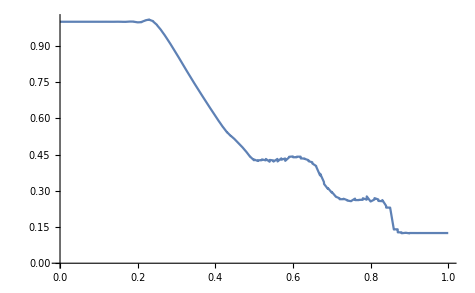
```mathematica
(*MUSCL, 100 cells*)
-Graphics-
```

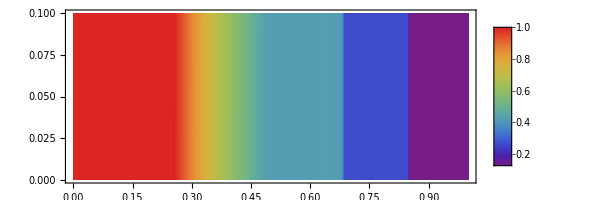

```mathematica
ListDensityPlot[Table[GetSolDensity[alpha,i,1],{i,1,nCells}],AspectRatio->Automatic,PlotRange->All,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```